## Лабораторная работа №7 Брич М.Н.

## Задание 1: Элементарная описательная статистика

```mathematica
data=RandomReal[{1,15},15] (* 14 случайных чисел от 14 до 50 *)
```

{9.58573,7.80155,1.11805,7.89996,6.49215,12.9389,11.4184,12.7136,11.4367,3.71866,10.5342,3.02149,12.5417,7.75462,4.65594}

```mathematica
Mean[data] (* Нахождение среднего значения *)
```

8.24212

```mathematica
Median[data](* Нахождение значения середины *)
```

7.89996

```mathematica
Max[data](* Нахождение максимального значения *)
```

12.9389

```mathematica
Variance[data](* Нахождение дисперсии - меры разброса между числами в наборе данных (SUM(x-mean)^2/length) *)
```

14.4882

```mathematica
StandardDeviation[data](* Нахождение среднеквадратичного отклонения (sqrt(Variance)) *)
```

3.80634

```mathematica
Quantile[data,1/2](* Нахождение квантиля. Её первым аргументом является набор данных;вторым аргументом является число в диапазоне от 0 до 1(т.е. процент) - гарантирует, что указанная часть набора будет меньше чем это число, остальные - больше или равно *)
```

7.89996

```mathematica
Quartiles[data](* Нахождение квартилей для списка - квантиль 1/4, 1/2, 3/4 *)
```

{5.11499,7.89996,11.4322}

## Задание 2: Работа со статистическими распределениями

```mathematica
NormalDistribution[μ,σ] (* Нормальное распределение *)
PDF[NormalDistribution[μ,σ],x] 

(* Вероятность получить 2 на графике *)
PDF[NormalDistribution[2,3],2]
```

NormalDistribution[μ,σ]

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(3 √(2 π))

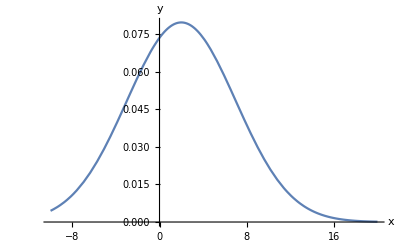

```mathematica
Plot[PDF[NormalDistribution[2,5],x],{x,-10,20}, AxesLabel->{x,y}] (* Визуализация функции плотности на графике при заданных значениях μ и σ *)
```

```mathematica
Mean[BinomialDistribution[120,.2]] (* Среднее значение для 120 попыток при биноминальном распределении с вероятностью успеха 0.2. Биноминальное распределение указывает сколько раз происходит некоторое событие в серии из n наблюдений с вероятносью успеха каждого события p *)
```

24.

```mathematica
(* Получение общей формулы характеристической функции для нормального распределения и распределения Коши, Как и функция распределения вероятности (PDF),характеристическая функция однозначно определяет распределение. *)
```

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t] 
CharacteristicFunction[CauchyDistribution[μ,σ],t]
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

ⅇ^(ⅈ t μ-t σ Sign[t])

```mathematica
(* Нахождение абсолютного момента для случайной переменной X в Пуассоновом распределении и рапределении Коши. Moment - ожидаемое значение переменной возведенной в n-ную степень *)
```

```mathematica
Moment[PoissonDistribution[μ],n] 
Moment[CauchyDistribution[μ,σ],n]
```

Piecewise[{{BellB[n,μ], n≥0}, {0, True}}]

Piecewise[{{1, n==0}, {Indeterminate, True}}]

```mathematica
(* Генерация случайных чисел из распределений *)
(* Возвращает список из n псевдослучайных чисел из указанного распределения *)
```

```mathematica
RandomVariate[ChiSquareDistribution[10],8] 
RandomVariate[PoissonDistribution[10],8]
RandomVariate[GeometricDistribution[2/4],17]
```

{16.1165,7.20804,14.5065,10.3154,5.85557,13.9542,15.3702,13.8647}

{10,15,7,10,11,12,14,16}

{0,0,0,0,0,0,1,0,2,7,2,1,0,0,2,0,5}

```mathematica
(* Генерация 10000 чисел из гамма-распределения *)
```

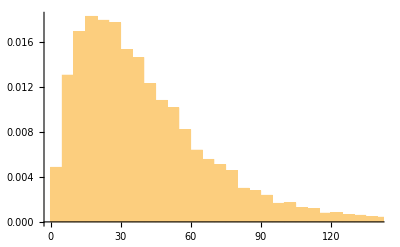

```mathematica
data=RandomVariate[GammaDistribution[2,20],10000];
(* Построение гистограммы для значений по шкале плотности вероятности *)
hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

```mathematica
(* Визуализация функции теоретической плотности *)
```

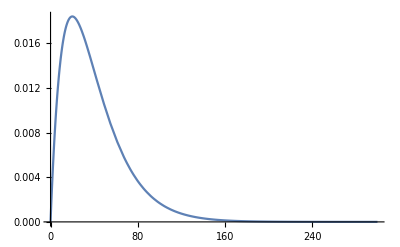

```mathematica
pl=Plot[PDF[GammaDistribution[2,20],x],{x,0,300}]
```

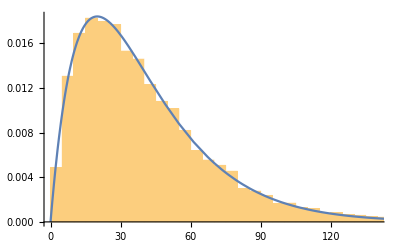

```mathematica
Show[hist,pl] (* Отображение двух графиков вместе *)
```

```mathematica
(* Часто требуется оценить значения параметра,исходя из предположения,что массив данных подчиняется определенному распределению. FindDestributionParameters - находит по полученым данным параметры распределения Поиск оценки максимального правдоподобия параметров: *)
```

```mathematica
alphabeta=FindDistributionParameters[data,GammaDistribution[α,β]]
```

{α→1.99134,β→20.2751}

```mathematica
gdist=EstimatedDistribution[data,GammaDistribution[α,β]] (* Находит исходные параметры объекта-распределения *)
```

GammaDistribution[1.99134,20.2751]

```mathematica
LogLikelihood[gdist,data] (* Вычисление логарифмического правдоподобия *)
```

-45835.3

```mathematica
(* Создание контурного графика в окрестности найденных значений, обеспечивающего качественное сравнение логарифмического правдоподобия, точки на определенной линии имеют одинаковое правдоподобие *)
```

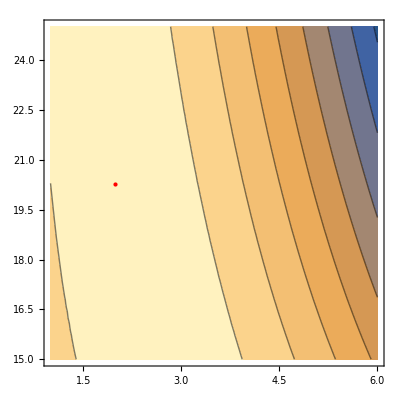

```mathematica
ContourPlot[LogLikelihood[GammaDistribution[α,β],data],{α,1,6},{β,15,25},Epilog->{Red,Point[{α,β}/.alphabeta]}]
```

## Задание 3: Проверка гипотез о математическом ожидании

```mathematica
<<HypothesisTesting`
```

```mathematica
(* Генерация набора данных *)
```

```mathematica
data = RandomVariate[NormalDistribution[1,3], 15]
```

{0.680868,-1.51089,5.21148,-2.48368,1.2756,-1.76929,-0.907799,5.57099,0.429472,3.56541,-1.04319,2.75988,1.87852,1.80392,-1.67699}

```mathematica
Mean[data]
```

0.918954

```mathematica
(* Выполнение t-теста, возвращает p-значение теста при нулевой гипотезе,что математическое ожидание равно среднему значению *)
```

```mathematica
TTest[data, 1]
```

0.903881

```mathematica
(* Выполнение t-теста при альтернативной гипотизе (на сколько переданное значение ближе к минимальному) *)
```

```mathematica
TTest[data, 1, AlternativeHypothesis->"Less"]
```

0.45194

```mathematica
data2 = RandomVariate[NormalDistribution[1,3],15]
(* t-тест, при котором учитывается равность средних значений этих наборов данных *)
TTest[{data,data2}]
```

{3.15318,1.31186,-2.1872,6.05654,1.03138,2.16596,-2.42974,3.7786,-0.0287684,-0.907526,-3.41047,3.88204,2.7551,4.50982,2.96897}

0.549995

```mathematica
Mean[data2]
```

1.70535

```mathematica
(* ... с учетом альтернативной гипотизы *)
```

```mathematica
TTest[{data, data2},-3,AlternativeHypothesis->"Less"]
```

0.98998

```mathematica
(* Вычисление парного t-критерия. Тестирует d1-d2 на равенство нулю *)
```

```mathematica
PairedTTest[{data,data2}]
```

0.567853

```mathematica
(* проверить,будет ли разница между двумя средними значениями существенно отличаться от предполагаемого значения. В этом случае,нулевой гипотезой является предположение,что математические ожидания равны (разность равна 0). При других значениях, например 4, проверяем, что математическое ожидание для data является в 4 раза больше чем дляdata2 *)
```

```mathematica
MeanDifferenceTest[data, data2,0]
```

OneSidedPValue→0.275016659345

```mathematica
MeanTest[data-data2,0] (* Парное сравнение наборов данных, получение попарных разностей *)
```

OneSidedPValue→0.2839263626085

## Задание 4: Работа со столбцами данных

```mathematica
(* Блок данных с локализированным генератором псевдослучайных чисел. 9 записей по 5 чисел от 0 до 5 в кортеже. команда SeedRandom обеспечивает предсказуемый результат *)
```

```mathematica
data = BlockRandom[SeedRandom[1];RandomInteger[5,{9,5}]]
```

{{4,2,4,0,1},{0,0,2,0,0},{3,5,2,0,3},{4,4,1,3,3},{4,1,4,2,1},{1,4,5,4,5},{0,3,3,0,0},{2,3,1,1,3},{2,5,1,1,4}}

```mathematica
MatrixForm[data] (* Создание матричной формы *)
```

(4 | 2 | 4 | 0 | 1
0 | 0 | 2 | 0 | 0
3 | 5 | 2 | 0 | 3
4 | 4 | 1 | 3 | 3
4 | 1 | 4 | 2 | 1
1 | 4 | 5 | 4 | 5
0 | 3 | 3 | 0 | 0
2 | 3 | 1 | 1 | 3
2 | 5 | 1 | 1 | 4)

```mathematica
Grid[data] (* Отображение матричной формы без скобок *)
```

4 | 2 | 4 | 0 | 1
0 | 0 | 2 | 0 | 0
3 | 5 | 2 | 0 | 3
4 | 4 | 1 | 3 | 3
4 | 1 | 4 | 2 | 1
1 | 4 | 5 | 4 | 5
0 | 3 | 3 | 0 | 0
2 | 3 | 1 | 1 | 3
2 | 5 | 1 | 1 | 4

```mathematica
Mean[data](* Среднее арифметическое каждого столбца *)
StandardDeviation[data] (* Среднеквадратическое отклонение ддя каждого столбца *)
Median[data] (* Поиск медианы для каждого столбца *)
```

{20/9,3,23/9,11/9,20/9}

{(√97)/6,√3,(√(41/2))/3,(√79)/6,(√115)/6}

{2,3,2,1,3}

```mathematica
col =data[[All, 2]](* Получение отдельного столбца *)
Mean[col]
StandardDeviation[col]
```

{2,0,5,4,1,4,3,3,5}

3

√3

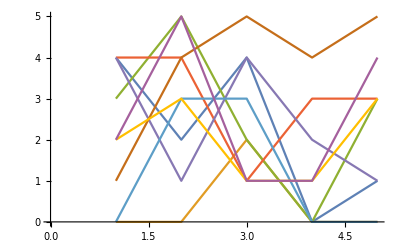

```mathematica
ListLinePlot[data] (* Визуализация группы данных с помощью дмуверного графика (столбец-значение)*)
```

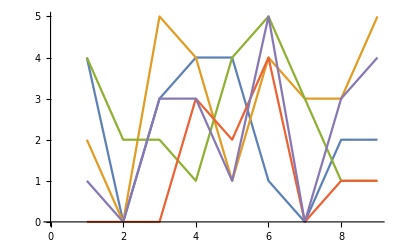

```mathematica
ListLinePlot[ Transpose[data]] (* Визуализация транспонированных(столбцы и строки меняются местами) данных *)
```

```mathematica
data222 = Map[Normalize,Transpose[data]] (* Map применяет normalize к каждой строчке транспонированной матрице *)
```

{{2 √(2/33),0,√(3/22),2 √(2/33),2 √(2/33),1/(√66),0,√(2/33),√(2/33)},{2/(√105),0,√(5/21),4/(√105),1/(√105),4/(√105),√(3/35),√(3/35),√(5/21)},{4/(√77),2/(√77),2/(√77),1/(√77),4/(√77),5/(√77),3/(√77),1/(√77),1/(√77)},{0,0,0,3/(√31),2/(√31),4/(√31),0,1/(√31),1/(√31)},{1/(√70),0,3/(√70),3/(√70),1/(√70),√(5/14),0,3/(√70),2 √(2/35)}}

```mathematica
data222[[1]]
```

{2 √(2/33),0,√(3/22),2 √(2/33),2 √(2/33),1/(√66),0,√(2/33),√(2/33)}

```mathematica
WolframAlpha[
```

```mathematica
Sqrt[#1^2+#2^2+#3^2+#4^2+#5^2+#6^2 +#7^2+#8^2+#9^2]& data222[[1]]
```

{2 √(2/33) (√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&),0,√(3/22) (√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&),2 √(2/33) (√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&),2 √(2/33) (√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&),(√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&)/(√66),0,√(2/33) (√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&),√(2/33) (√(#1^2+#2^2+#3^2+#4^2+#5^2+#6^2+#7^2+#8^2+#9^2)&)}

```mathematica
Transpose[%] (* Транспонирование результата, получив матрицу с нормализованными столбцами *)
```

{{2 √(2/33),2/(√105),4/(√77),0,1/(√70)},{0,0,2/(√77),0,0},{√(3/22),√(5/21),2/(√77),0,3/(√70)},{2 √(2/33),4/(√105),1/(√77),3/(√31),3/(√70)},{2 √(2/33),1/(√105),4/(√77),2/(√31),1/(√70)},{1/(√66),4/(√105),5/(√77),4/(√31),√(5/14)},{0,√(3/35),3/(√77),0,0},{√(2/33),√(3/35),1/(√77),1/(√31),3/(√70)},{√(2/33),√(5/21),1/(√77),1/(√31),2 √(2/35)}}

```mathematica
Map[Max,Transpose[data]](* Пример транспонирования и применения преобразований для функций, которые выравнивают свой аргумент. Применяет Max к каждой строчке Транспонированной матрицы, аналогично взятию по столбцам *)
```

{4,5,5,4,5}

## Задание 5: Выполнение операций с подгруппами данных

```mathematica
(* Задание урожайности для 3 типов грунта и 2 типов семян, цифры - урожайности *)
```

```mathematica
agdata={{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{sandy,seedA,168},{clay,seedA,184},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{clay,seedA,186},{silty,seedB,174},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{sandy,seedA,182},{sandy,seedB,177},{silty,seedA,180},{clay,seedB,175},{silty,seedB,181},{sandy,seedA,176},{silty,seedB,190}};
```

```mathematica
bySoilType=GatherBy[agdata,First] (* Собираем в группы по первому элементу каждой точки данных *)
```

{{{clay,seedB,175},{clay,seedB,165},{clay,seedA,184},{clay,seedA,186},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{clay,seedB,175}},{{silty,seedB,180},{silty,seedB,174},{silty,seedA,180},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{sandy,seedA,182},{sandy,seedB,177},{sandy,seedA,176}}}

```mathematica
(* Вывод типа грунта и средней урожайности для каждой группы. x[[1,1] - взять название. N[Mean[x[[All,3]]]] - взять среднее значение для каждого типа грунта *)
```

```mathematica
Table[{x[[1,1]],N[Mean[x[[All,3]]]]},{x,bySoilType}]
```

{{clay,180.},{silty,181.},{sandy,176.571}}

```mathematica
(* Группировка данных по второму элементу каждой строки, получаем информацию об урожайности в зависимости от сорта семян. Перебираем все элементы из agdata и берём второй элемент каждой записи, группируем по нему *)
```

```mathematica
bySeedType=GatherBy[agdata,#[[2]]&]
```

{{{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{sandy,seedB,171},{sandy,seedB,173},{silty,seedB,174},{sandy,seedB,177},{clay,seedB,175},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{clay,seedA,184},{sandy,seedA,189},{clay,seedA,186},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{sandy,seedA,182},{silty,seedA,180},{sandy,seedA,176}}}

```mathematica
(* Вычисление средней урожайности для каждого сорта семян *)
```

```mathematica
Table[{x[[1,2]],N[Mean[x[[All,-1]]]]},{x,bySeedType}]
```

{{seedB,176.1},{seedA,182.}}

```mathematica
(* Узнаем диапазон урожайности и вычисляем минимальную и максимальную урожайость для каждого сорта семян *)
```

```mathematica
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,bySeedType}]
```

{{seedB,{165.,190.}},{seedA,{168.,192.}}}

```mathematica
(* Метаданные о лекарствах, возрасте пациента и времени выздоровления*)
```

```mathematica
meddata={{drugB,67,18},{drugB,48,18},{drugA,33,16},{drugB,76,33},{drugB,33,3},{placebo,40,15},{drugB,78,28},{drugB,54,13},{placebo,46,23},{drugA,36,12},{drugA,69,30},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24},{placebo,25,9},{drugB,75,25},{drugB,22,3},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34},{drugB,52,16}};
```

```mathematica
byDrug=GatherBy[meddata,First] (* Группировка данных по виду лекарств *)
describe[values_]:={Length[values],Mean[values],Median[values],{Min[values],Max[values]}} (* Получение размера выборки, среднего, медианы и диапазона для выбранного списка *)
```

{{{drugB,67,18},{drugB,48,18},{drugB,76,33},{drugB,33,3},{drugB,78,28},{drugB,54,13},{drugB,75,25},{drugB,22,3},{drugB,52,16}},{{drugA,33,16},{drugA,36,12},{drugA,69,30},{drugA,78,40},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,40,15},{placebo,46,23},{placebo,77,37},{placebo,25,9},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}}}

```mathematica
(* Получение статистических результатов в разрезе вида лекарства *)
```

```mathematica
Table[{x[[1,1]],describe[N[x[[All,3]]]]},{x,byDrug} ]
```

{{drugB,{9,17.4444,18.,{3.,33.}}},{drugA,{8,24.,21.,{12.,40.}}},{placebo,{8,21.375,21.5,{8.,37.}}}}

```mathematica
(* Группировка по возрасту (каждые 10 лет) *)
```

```mathematica
byAgeGroup=GatherBy[meddata,IntegerPart[#[[2]]/10]&]
```

{{{drugB,67,18},{drugA,69,30},{placebo,69,34}},{{drugB,48,18},{placebo,40,15},{placebo,46,23},{drugA,45,16},{placebo,47,20}},{{drugA,33,16},{drugB,33,3},{drugA,36,12},{drugA,36,18}},{{drugB,76,33},{drugB,78,28},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugB,75,25}},{{drugB,54,13},{drugA,58,24},{placebo,51,25},{drugB,52,16}},{{placebo,25,9},{drugB,22,3},{placebo,27,8}}}

```mathematica
(* Вычисление статистических данных в разрезе возрастных групп *)
```

```mathematica
Table[{10IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byAgeGroup}]//Sort
```

{{20,{3,6.66667,8.,{3.,9.}}},{30,{4,12.25,14.,{3.,18.}}},{40,{5,18.4,18.,{15.,23.}}},{50,{4,19.5,20.,{13.,25.}}},{60,{3,27.3333,30.,{18.,34.}}},{70,{6,33.1667,34.5,{25.,40.}}}}

```mathematica
(* Группировка по виду лекарств и возрастной группе *)
```

```mathematica
byDrugAndAgeGroup=GatherBy[meddata,{First[#],IntegerPart[#[[2]]/10]}&]
```

{{{drugB,67,18}},{{drugB,48,18}},{{drugA,33,16},{drugA,36,12},{drugA,36,18}},{{drugB,76,33},{drugB,78,28},{drugB,75,25}},{{drugB,33,3}},{{placebo,40,15},{placebo,46,23},{placebo,47,20}},{{drugB,54,13},{drugB,52,16}},{{drugA,69,30}},{{drugA,78,40},{drugA,79,36}},{{placebo,77,37}},{{drugA,45,16}},{{drugA,58,24}},{{placebo,25,9},{placebo,27,8}},{{drugB,22,3}},{{placebo,51,25}},{{placebo,69,34}}}

```mathematica
(* Произведена сортировка по виду лекарств и данные отображены в виде таблицы при помощи Grid *)
```

```mathematica
Table[{x[[1,1]],10IntegerPart[x[[1,2]]/10],describe[N[x[[All,-1]]]]},{x,byDrugAndAgeGroup}]//Sort//Grid
```

drugA | 30 | {3,15.3333,16.,{12.,18.}}
drugA | 40 | {1,16.,16.,{16.,16.}}
drugA | 50 | {1,24.,24.,{24.,24.}}
drugA | 60 | {1,30.,30.,{30.,30.}}
drugA | 70 | {2,38.,38.,{36.,40.}}
drugB | 20 | {1,3.,3.,{3.,3.}}
drugB | 30 | {1,3.,3.,{3.,3.}}
drugB | 40 | {1,18.,18.,{18.,18.}}
drugB | 50 | {2,14.5,14.5,{13.,16.}}
drugB | 60 | {1,18.,18.,{18.,18.}}
drugB | 70 | {3,28.6667,28.,{25.,33.}}
placebo | 20 | {2,8.5,8.5,{8.,9.}}
placebo | 40 | {3,19.3333,20.,{15.,23.}}
placebo | 50 | {1,25.,25.,{25.,25.}}
placebo | 60 | {1,34.,34.,{34.,34.}}
placebo | 70 | {1,37.,37.,{37.,37.}}

## Задание 6: Замена или удаление недостающих или недействительных данных

```mathematica
(* возврат ввп для каждой страны, внесенной в перечень CountyData *)
```

```mathematica
gdps=Map[CountryData[#,"GDP"]&,CountryData[All]];
```

```mathematica
(* берем первые 10 записей *)
```

```mathematica
Take[gdps,10]
```

{1.98071×10^10 $,Missing[NotAvailable],1.47996×10^10 $,1.45164×10^11 $,6.38×10^8 $,3.15507×10^9 $,6.23069×10^10 $,2.11174×10^8 $,1.41506×10^9 $,3.83067×10^11 $}

```mathematica
(* попытка взять максимум (для некоторых стран эти данные могут быть недоступны) *)
```

```mathematica
Max[gdps]
```

Max::nord2: Comparison of 2.09366×10^13 and -∞ is invalid.

Max[Missing[NotAvailable],2.09366×10^13 $]

```mathematica
(* произведем подсчет Missing данных *)
```

```mathematica
Count[gdps,_Missing]
```

16

```mathematica
(* общее количество записей *)
```

```mathematica
Length[gdps]
```

249

```mathematica
(* удаление тех записей, которые отсутсвуют *)
```

```mathematica
filteredgdps=DeleteCases[gdps,_Missing];
```

```mathematica
{Length[filteredgdps],Max[filteredgdps]}
```

{233,2.09366×10^13 $}

```mathematica
(* задаем новый датасет *)
```

```mathematica
data={{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{4,88.6,1.9},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}};
```

```mathematica
(* отображение данных в табличной форме *)
```

```mathematica
Grid[data,Dividers->All]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
4 | 88.6 | 1.9
1 | 62.3 | 1.8
1 | 82.7 | NA
1 | 35.5 | 1.84

```mathematica
(* функция идентифицирует такие элементы данных, проверяя соответствие данных заданному шаблону.Она возвращает значение true, если данные на входе не совпадают с шаблоном. Действительные элементы этого набора данных должны содержать 1 или 2 в качестве первого элемента и числа в качестве второго и третьего элемента.Шаблон для данных такого типа будет следующим:{1|2, _?NumberQ, _?NumberQ}.Символ|указывает на альтернативу:первый элемент должен быть 1 или 2. Функция NumberQ проверяет,является ли ее аргумент числом,а выражение_?NumberQ является шаблоном для чисел.Можно использовать этот шаблон вместе с функциямиMatchQиNot,чтобы сформулировать функцию,которая идентифицирует неверные элементы данных. *)
```

```mathematica
baddata[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]]
DeleteCases[data,_?baddata] (* удаление по образцу *)
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,35.5,1.84}}

```mathematica
(* задали функцию, определяющую является ли запись набора данных недействительной, путем проверки соответствия первого элемента записи значениям 1 или 2 *)
```

```mathematica
badgroup[entry_]:=Not[MatchQ[entry[[1]],1|2]]
filtereddata=DeleteCases[data,_?badgroup] (* удаление по образцу *)
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(* выборка данных элементов группы 1 *)
```

```mathematica
group1=Select[filtereddata,#[[1]]===1&]
```

{{1,71.6,0.41},{1,46.,2.72},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(* выборка чисел из последнего элемента каждой записи (3 столбец), рассчет среднего значения, NumberQ без _? потому что Select вторым параметром принимает критерий *)
```

```mathematica
group1mean=Mean[Select[group1[[All,-1]],NumberQ]]
```

2.104

```mathematica
(* подставление вместо NA найденное среднее значение *)
```

```mathematica
filtereddata[[All,3]]=filtereddata[[All,3]]/."NA"->group1mean
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}

```mathematica
(* отображение отфильтрованных данных таблично *)
```

```mathematica
Grid[filtereddata,Dividers->All]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 2.104
1 | 35.5 | 1.84

```mathematica
(* Функция группирует по заданному столбцу и заменяет любое нечисленное значение в обрабатываемом столбце результатом указанной функциию. имя набора данных,номер подлежащего обработке столбца,номер столбца для группировки и функцию,используемую для обработки элементов столбца. *)
```

```mathematica
replaceByGroup[data_,col_,groupcol_,f_]:=Block[{columnvals,funvals,grouped,groups,rules},columnvals=data[[All,{groupcol,col}]];
If[VectorQ[columnvals[[All,2]],NumericQ],
columnvals[[All,2]],
grouped=GatherBy[columnvals,First];
groups=grouped[[All,1,1]];
funvals=Table[f[Select[grouped[[i]][[All,2]],NumericQ]],{i,Length[groups]}];
rules=Table[Rule[{groups[[i]],_?(Not[NumericQ[#]]&)},{groups[[i]],funvals[[i]]}],{i,Length[groups]}];
Replace[columnvals,rules,{1}][[All,2]]]]
```

```mathematica
(* Определяем новые данных *)
newdata=DeleteCases[data,_?badgroup]
```

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,NA},{1,35.5,1.84}}

```mathematica
(* замена нечисленных данных в 3-м столбце средним от соответствующей группы *)
```

```mathematica
replaceByGroup[newdata,3,1,Mean]
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}

```mathematica
(* замена медианой *)
```

```mathematica
replaceByGroup[newdata,3,1,Median]
```

{0.41,4.96,0.18,2.72,1.06,3.75,1.8,1.84,1.84}

```mathematica
(* отображение "очищенного" набора данных в табличной форме *)
```

```mathematica
Grid[Transpose[Table[If[j==1,newdata[[All,j]],replaceByGroup[newdata,j,1,Mean]],{j,Length[newdata[[1]]]}]]]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 2.104
1 | 35.5 | 1.84

```mathematica
(* недействительные элементы второго столбца заменены средним от соответствующей группы второго столбца,а недействительные элементы третьего столбца заменены медианой от соответствующей группы третьего столбца *)
```

```mathematica
Grid[Transpose[{newdata[[All,1]],replaceByGroup[newdata,2,1,Mean],replaceByGroup[newdata,3,1,Median]}]]
```

1 | 71.6 | 0.41
2 | 27.2 | 4.96
2 | 59.3 | 0.18
1 | 46. | 2.72
2 | 42.2 | 1.06
1 | 89.1 | 3.75
1 | 62.3 | 1.8
1 | 82.7 | 1.84
1 | 35.5 | 1.84

## Задание 7: Выполнение линейной регрессии

```mathematica
(* формирование набора данных *)
```

```mathematica
data = Table[{2 + i + RandomReal[{-3, 8}], i + RandomReal[{-2, 6}]}, {i, 0, 30}];model=LinearModelFit[data,x,x] (* создание линейной модели заданного набора данных *)
```

FittedModel[-0.302025+0.847953 x]

```mathematica
model["BestFit"] (* извлечение функциональной формы модели *)
```

-0.302025+0.847953 x

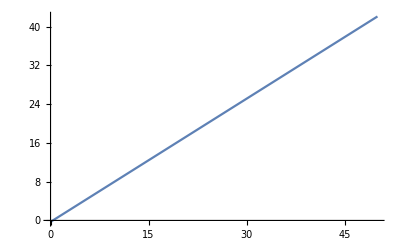

```mathematica
Plot[model["BestFit"], {x, 0, 50}] (* визуализация функциональной формы модели *)
```

```mathematica
(* отображение данных и линии наилучшего соответствия *)
```

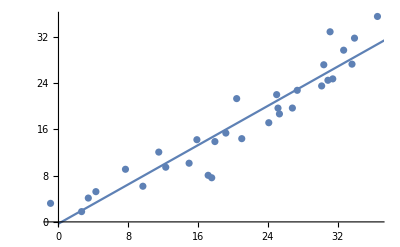

```mathematica
Show[ListPlot[data], Plot[model["BestFit"], {x, 0, 50}]]
```

```mathematica
model["ParameterTable"] (* получаем информацию по оценке параметров выполненной регрессии *)
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.302025 | 1.26467 | -0.238818 | 0.812926
x | 0.847953 | 0.0548355 | 15.4636 | 1.52795×10^-15

```mathematica
(* отображение нормализованных и наблюдаемых невязок *)
```

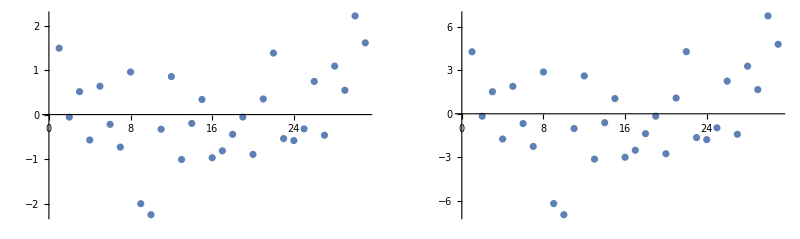

```mathematica
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}];
{{ListPlot[sr], ListPlot[fr]}}//GraphicsGrid
```

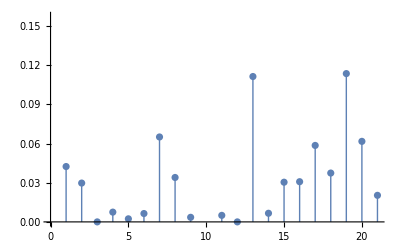

```mathematica
ListPlot[model["CookDistances"], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick] (* график расстояний Кука - показывает разницу между вычисленными коэффициентами уравнения регриссии и значениями которые получились бы при исключении соответствующего наблюдения *)
```

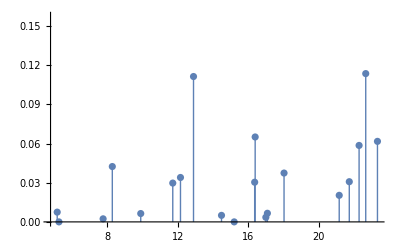

```mathematica
ListPlot[Transpose[{data[[All, 1]], model["CookDistances"]}], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick] (* график расстояний Кука в зависимости от предикторного значения *)
```

```mathematica
model["Properties"] (* предоставляемые свойства модели *)
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}